```mathematica
Table[NullBaseCoeff[ ChromaticPolynomial[CompleteGraph[k],x]],{k,1,10}]//TableForm
```

0 | 1 |  |  |  |  |  |  |  |  | 
0 | -1 | 1 |  |  |  |  |  |  |  | 
0 | 2 | -3 | 1 |  |  |  |  |  |  | 
0 | -6 | 11 | -6 | 1 |  |  |  |  |  | 
0 | 24 | -50 | 35 | -10 | 1 |  |  |  |  | 
0 | -120 | 274 | -225 | 85 | -15 | 1 |  |  |  | 
0 | 720 | -1764 | 1624 | -735 | 175 | -21 | 1 |  |  | 
0 | -5040 | 13068 | -13132 | 6769 | -1960 | 322 | -28 | 1 |  | 
0 | 40320 | -109584 | 118124 | -67284 | 22449 | -4536 | 546 | -36 | 1 | 
0 | -362880 | 1026576 | -1172700 | 723680 | -269325 | 63273 | -9450 | 870 | -45 | 1

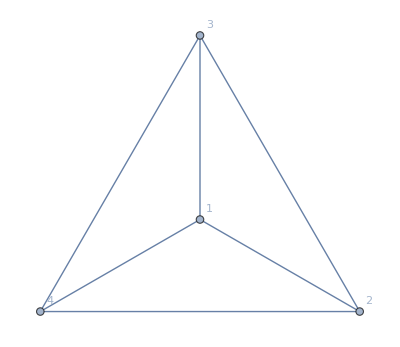

```mathematica
g=CompleteGraph[4,VertexLabels->"Name"]
```

```mathematica
TableForm[Table[ChromaticPolynomial[EdgeDelete[g,DeleteDuplicates[{e,e2}]],4]/24,{e,EdgeList[g]},{e2,EdgeList[g]}],TableHeadings->{EdgeList[g], EdgeList[g]}]
```

| 1<->2 | 1<->3 | 1<->4 | 2<->3 | 2<->4 | 3<->4
1<->2 | 2 | 3 | 3 | 3 | 3 | 7/2
1<->3 | 3 | 2 | 3 | 3 | 7/2 | 3
1<->4 | 3 | 3 | 2 | 7/2 | 3 | 3
2<->3 | 3 | 3 | 7/2 | 2 | 3 | 3
2<->4 | 3 | 7/2 | 3 | 3 | 2 | 3
3<->4 | 7/2 | 3 | 3 | 3 | 3 | 2

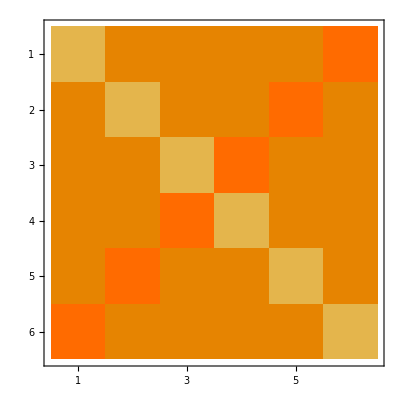

```mathematica
MatrixPlot[Table[ChromaticPolynomial[EdgeDelete[g,DeleteDuplicates[{e,e2}]],4]/24,{e,EdgeList[g]},{e2,EdgeList[g]}]]
```

```mathematica
s=Subsets[Range[4],{2}]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
With[
{size=5},
With[
{s=Subsets[Range[size],{2}]},TableForm[Tally[Table[CompleteBaseCoeff[ChromaticPolynomial[Graph[Range[size],sub],x]],{sub,Subsets[s,{1,Length[s]}]}]]//Sort,TableDepth->1]
]]
```

{{0,0,0,0,0,1},1}
{{0,0,0,0,1,1},10}
{{0,0,0,0,2,1},30}
{{0,0,0,0,3,1},20}
{{0,0,0,0,4,1},5}
{{0,0,0,1,2,1},15}
{{0,0,0,1,3,1},70}
{{0,0,0,2,3,1},30}
{{0,0,0,2,4,1},135}
{{0,0,0,3,4,1},60}
{{0,0,0,3,5,1},30}
{{0,0,0,4,5,1},150}
{{0,0,0,5,5,1},12}
{{0,0,0,6,6,1},70}
{{0,0,0,9,7,1},10}
{{0,0,1,4,4,1},10}
{{0,0,1,5,5,1},60}
{{0,0,1,7,6,1},125}
{{0,0,2,7,6,1},15}
{{0,0,2,10,7,1},110}
{{0,0,4,14,8,1},45}
{{0,0,8,19,9,1},10}

```mathematica
With[
{size=4},
With[
{s=Subsets[Range[size],{2}]},TableForm[Tally[Table[CompleteBaseCoeff[ChromaticPolynomial[Graph[Range[size],sub],x]],{sub,Subsets[s,{1,Length[s]}]}]]//Sort,TableDepth->1]
]]
```

{{0,0,0,0,1},1}
{{0,0,0,1,1},6}
{{0,0,0,2,1},12}
{{0,0,0,3,1},4}
{{0,0,1,2,1},3}
{{0,0,1,3,1},16}
{{0,0,2,4,1},15}
{{0,0,4,5,1},6}

```mathematica
With[
{size=3},
With[
{s=Subsets[Range[size],{2}]},TableForm[Tally[Table[CompleteBaseCoeff[ChromaticPolynomial[Graph[Range[size],sub],x]],{sub,Subsets[s,{1,Length[s]}]}]]//Sort,TableDepth->1]
]]
```

{{0,0,0,1},1}
{{0,0,1,1},3}
{{0,0,2,1},3}

```mathematica
With[
{size=2},
With[
{s=Subsets[Range[size],{2}]},TableForm[Tally[Table[CompleteBaseCoeff[ChromaticPolynomial[Graph[Range[size],sub],x]],{sub,Subsets[s,{1,Length[s]}]}]]//Sort,TableDepth->1]
]]
```

{{0,0,1},1}

```mathematica
With[
{size=6},
With[
{s=Subsets[Range[size],{2}]},TableForm[Tally[Table[CompleteBaseCoeff[ChromaticPolynomial[Graph[Range[size],sub],x]],{sub,Subsets[s,{1,Length[s]}]}]]//Sort,TableDepth->1]
]]
```

{{0,0,0,0,0,0,1},1}
{{0,0,0,0,0,1,1},15}
{{0,0,0,0,0,2,1},60}
{{0,0,0,0,0,3,1},60}
{{0,0,0,0,0,4,1},30}
{{0,0,0,0,0,5,1},6}
{{0,0,0,0,1,2,1},45}
{{0,0,0,0,1,3,1},200}
{{0,0,0,0,2,3,1},180}
{{0,0,0,0,2,4,1},585}
{{0,0,0,0,3,4,1},420}
{{0,0,0,0,3,5,1},300}
{{0,0,0,0,4,4,1},90}
{{0,0,0,0,4,5,1},900}
{{0,0,0,0,4,6,1},60}
{{0,0,0,0,5,5,1},432}
{{0,0,0,0,6,6,1},960}
{{0,0,0,0,7,6,1},180}
{{0,0,0,0,8,7,1},180}
{{0,0,0,0,9,7,1},360}
{{0,0,0,0,12,8,1},135}
{{0,0,0,0,16,9,1},15}
{{0,0,0,1,3,3,1},15}
{{0,0,0,1,4,4,1},240}
{{0,0,0,1,5,5,1},720}
{{0,0,0,1,6,5,1},360}
{{0,0,0,1,7,6,1},1215}
{{0,0,0,1,8,6,1},360}
{{0,0,0,2,6,5,1},225}
{{0,0,0,2,7,5,1},60}
{{0,0,0,2,7,6,1},450}
{{0,0,0,2,8,6,1},1260}
{{0,0,0,2,9,6,1},60}
{{0,0,0,2,10,7,1},2460}
{{0,0,0,2,11,7,1},180}
{{0,0,0,3,9,6,1},360}
{{0,0,0,3,9,7,1},90}
{{0,0,0,3,11,7,1},1440}
{{0,0,0,3,13,8,1},420}
{{0,0,0,4,9,6,1},90}
{{0,0,0,4,11,7,1},900}
{{0,0,0,4,12,7,1},360}
{{0,0,0,4,14,8,1},2700}
{{0,0,0,5,12,7,1},360}
{{0,0,0,5,15,8,1},360}
{{0,0,0,6,14,8,1},180}
{{0,0,0,6,15,8,1},1980}
{{0,0,0,6,18,9,1},910}
{{0,0,0,7,16,8,1},180}
{{0,0,0,8,19,9,1},2160}
{{0,0,0,9,19,9,1},360}
{{0,0,0,9,23,10,1},90}
{{0,0,0,10,20,9,1},360}
{{0,0,0,12,24,10,1},1140}
{{0,0,0,15,25,10,1},72}
{{0,0,0,18,30,11,1},240}
{{0,0,0,27,37,12,1},20}
{{0,0,1,6,11,6,1},10}
{{0,0,1,7,13,7,1},90}
{{0,0,1,8,13,7,1},15}
{{0,0,1,8,16,8,1},180}
{{0,0,1,9,16,8,1},300}
{{0,0,1,10,20,9,1},60}
{{0,0,1,11,20,9,1},1080}
{{0,0,1,15,25,10,1},1296}
{{0,0,2,13,20,9,1},60}
{{0,0,2,16,25,10,1},405}
{{0,0,2,22,31,11,1},1080}
{{0,0,4,23,31,11,1},45}
{{0,0,4,32,38,12,1},435}
{{0,0,8,46,46,13,1},105}
{{0,0,16,65,55,14,1},15}

```mathematica
With[
{size=7},
With[
{s=Subsets[Range[size],{2}]},TableForm[Tally[Table[CompleteBaseCoeff[ChromaticPolynomial[Graph[Range[size],sub],x]],{sub,Subsets[s,{1,Length[s]}]}]]//Sort,TableDepth->1]
]]
```

$Aborted

```mathematica
Table[
{k,Max[CompleteBaseCoeff[ChromaticPolynomial[Graph[Range[k],{1<->2}],x]]]},
{k,1,10}
]//TableForm
```

1 | 1
2 | 1
3 | 2
4 | 5
5 | 19
6 | 65
7 | 285
8 | 1351
9 | 6069
10 | 35574